```mathematica
(*初始化删除变量及设定目录*)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*示意图*)
-Graphics-
```

-Graphics-

```mathematica
(*设定变量*)
dx=D[x[t], t];
dθ=D[θ[t], t];
ddx=D[dx, t];
ddθ=D[dθ, t];
in=m l^2/3;(*摆转动惯量I*)

(*设定参数*)
parameter={M->1.096,m->0.109,l->0.25,g->-9.8}

(*一阶倒立摆微分方程*)
equ={
ddx==(m^2 g l^2/(in(M+m)+M m l^2)) θ[t]+((in+m l^2)/(in(M+m)+M m l^2)) τ,
ddθ==(m g l(M+m)/(in(M+m)+M m l^2))θ[t]+(m l/(in(M+m)+M m l^2))τ
}/.parameter;
```

{M→1.096,m→0.109,l→0.25,g→-9.8}

x''=(m^2 gl^2)/(I(M+m)+Mml^2)θ+(I+ml^2)/(I(M+m)+Mml^2)u
θ''=(mgl(M+m))/(I(M+m)+Mml^2)θ+ml/(I(M+m)Mml^2)u

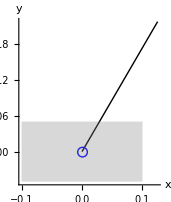

```mathematica
(*建模*)
Graphics[
{
Thick,Line[{{x[t],0},{x[t]+l Sin[θ[t]],l Cos[θ[t]]}}],
Blue,Sphere[{x[t],0},0.008],
Gray,Opacity[0.3],Rectangle[{x[t]-0.1,-0.05},{x[t]+0.1,0.05}]
},Axes->True,AxesLabel->{x,y,z}
]/.{x[t]->0 Pi/180,θ[t]->30 Pi/180}~Join~parameter
```

```mathematica
(*PID控制器*)
Kp=1 10^-0;
Kv=8 10^-2;
xd=0;(*目标位移*)
dxd=0 10^-5;(*目标速度*)
(*输入力矩*)
τ=pid=(M )(ddx+Kv(dxd-dx)+Kp(xd-x[t]))/.parameter;
```

```mathematica
(*模拟时长*)
finishtime=20.0;(*The simulation time from 0 to the finishtime*)
(*初始条件设定*)
initial={x[0]==0,θ[0]==180Pi/180,x'[0]==0,θ'[0]==0};
Monitor[
data=NDSolve[{equ,initial},{x[t],θ[t]},{t,0,finishtime},SolveDelayed -> True,EvaluationMonitor:>(indicatortime=t;)],
"t="Dynamic[indicatortime,UpdateInterval->1]];
```

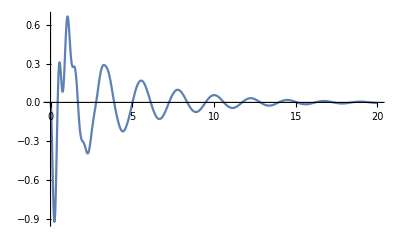

```mathematica
(*小车位移图*)
Plot[Evaluate[x[t]/.data],{t,0,finishtime},PlotRange->All,PlotLegends->x[t]]
```

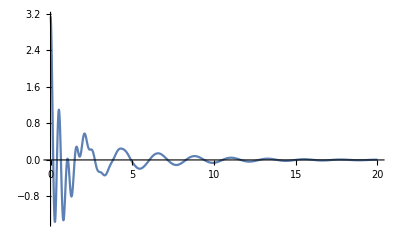

```mathematica
(*杆角度变化*)
Plot[Evaluate[θ[t]/.data],{t,0,finishtime},PlotRange->All,PlotLegends->θ[t]]
```

```mathematica
(*动画*)
frame=Table[
Graphics[
{
Thick,Line[{{x[t],0},{x[t]+l Sin[θ[t]],l Cos[θ[t]]}}],
Blue,Sphere[{x[t],0},0.008],
Gray,Opacity[0.3],Rectangle[{x[t]-0.1,-0.05},{x[t]+0.1,0.05}]
},Axes->True,AxesLabel->{x,y,z},PlotRange->{{-1.0,1.0},{-.5,.5}}
]/.parameter~Join~First@data,{t,0,finishtime,finishtime/100}];
```

```mathematica
ListAnimate[frame,24,AnimationRunning->True]
```

```mathematica
(*动画输出至当前目录下*)
If[False,Export["Simulation"<>DateString["ISODate"]<>".gif",frame,"DisplayDurations"->0.05]]
```

Simulation2019-07-12.gif